```mathematica
Matches[g_]:=Block[{i, vertexList},
vertexList = VertexList[g];
For[i=1,i≤Length[vertexList],i++,
If[OddQ[VertexDegree[g,vertexList[[i]]]],
Return[False]
]
];
Return[True]
]
```

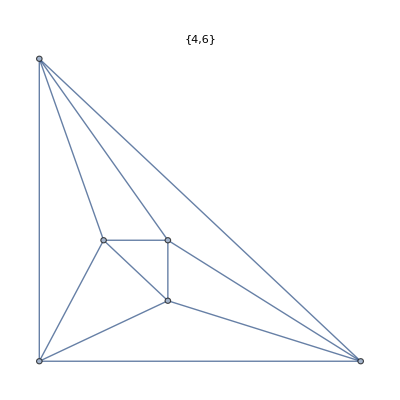
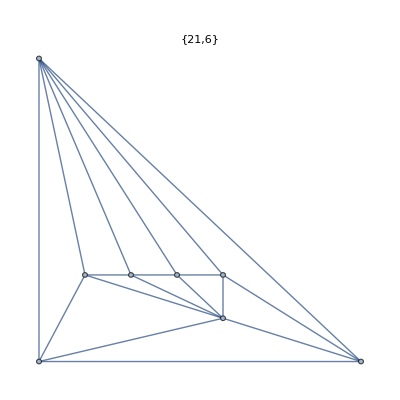
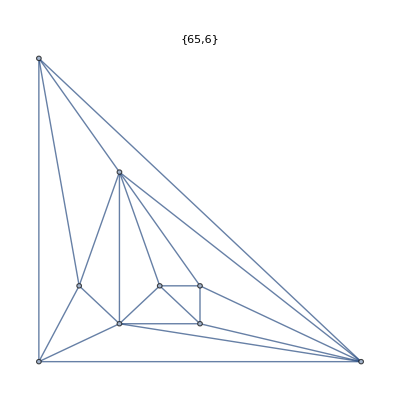
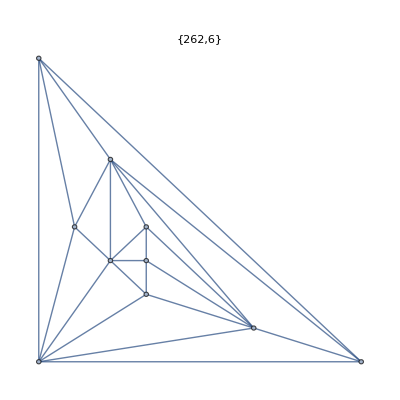
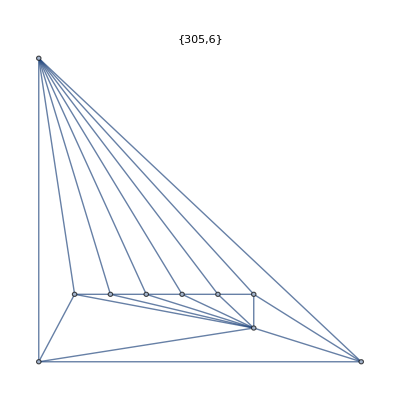
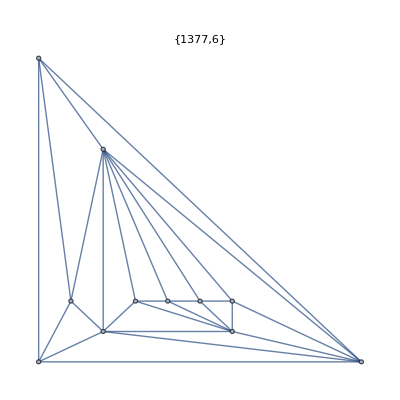
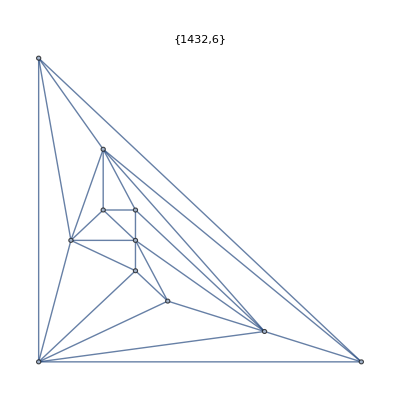
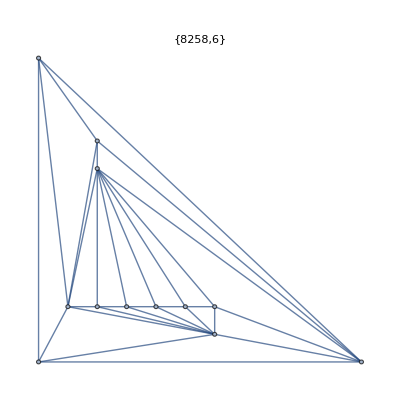

```mathematica
Monitor[
Select[
Table[
With[{g=ReadGrof[k]},Graph[g,GraphLayout->"PlanarEmbedding",PlotLabel->{k,ChromaticPolynomial[g,3]}]
],
{k,1,50000}
],
Matches[#]&
],
k]
```

```mathematica
FindClique[ReadGrof[1],{5},1]
```

{}